```mathematica
SetDirectory[NotebookDirectory[]];
```

## Tools

```mathematica
CutLow[lower_,list_,source_]:=For[i=1,i≤Length[source],++i,If[sizes⟦i⟧≥lower,AppendTo[newsizes,sizes⟦i⟧],Null]]
```

```mathematica
CutHigh[higher_,list_,source_]:=For[i=1,i≤Length[source],++i,If[sizes⟦i⟧≤higher,AppendTo[newsizes,sizes⟦i⟧],Null]]
```

## Import data

```mathematica
distribution=Import["distribution.csv"];
```

```mathematica
dims=Import["dims.csv"];
totalSites=dims⟦1⟧⟦1⟧dims⟦2⟧⟦1⟧;
```

```mathematica
sites=Table[distribution⟦i⟧⟦1⟧,{i,1,Length[distribution]}];
counts=Table[distribution⟦i⟧⟦2⟧,{i,1,Length[distribution]}];
```

## Analysis

```mathematica
sum=0;
total=Total[distribution]⟦2⟧;
cumulative={};
For[i=1,i<Length[distribution],++i,AppendTo[cumulative,{distribution⟦i⟧⟦1⟧,total-sum+distribution⟦i⟧⟦2⟧}];sum=sum+distribution⟦i⟧⟦2⟧]
```

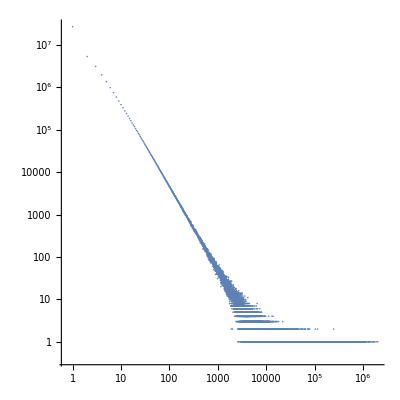

```mathematica
ListLogLogPlot[distribution,PlotRange->All,AspectRatio->1]
```

Cumulative plot

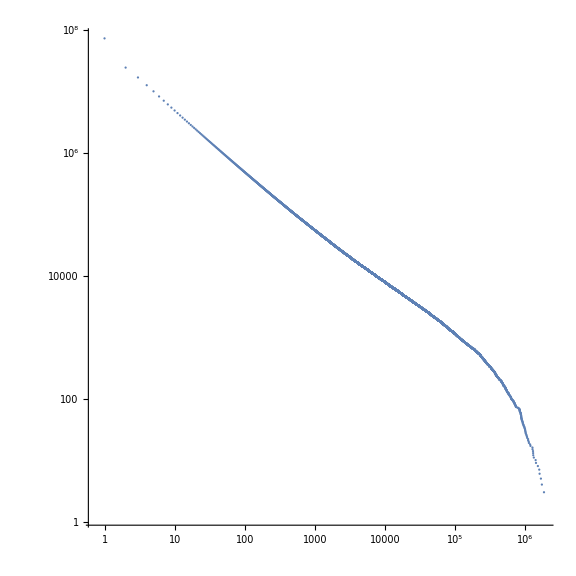

```mathematica
ListLogLogPlot[cumulative,ImageSize->Large,PlotRange->All,AspectRatio->1]
```

Plot of [ Size of cluster vs. Fraction of the total volume clusters of this size comprise ]

```mathematica
volume=Table[{distribution⟦i⟧⟦1⟧,(distribution⟦i⟧⟦1⟧*distribution⟦i⟧⟦2⟧)/totalSites},{i,1,Length[distribution]}];
```

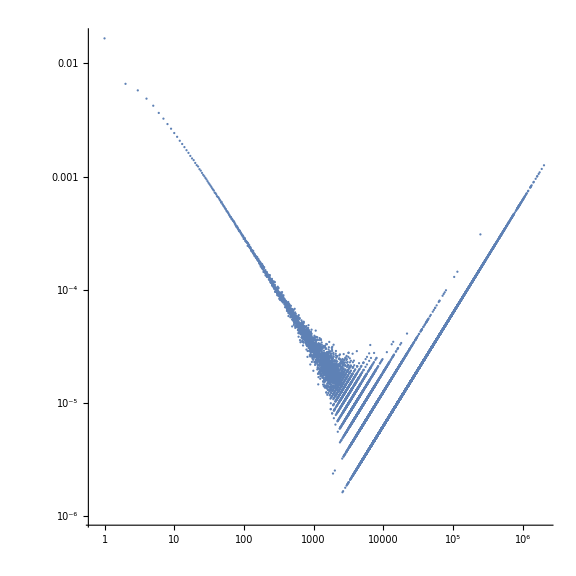

```mathematica
ListLogLogPlot[volume,ImageSize->Large,PlotRange->All,AspectRatio->1]
```

```mathematica
sum=0;
totalV=Total[volume]⟦2⟧;
cumulativeVolume={};
For[i=1,i<Length[volume],++i,AppendTo[cumulativeVolume,{volume⟦i⟧⟦1⟧,totalV-sum+volume⟦i⟧⟦2⟧//N}];sum=sum+volume⟦i⟧⟦2⟧]
```

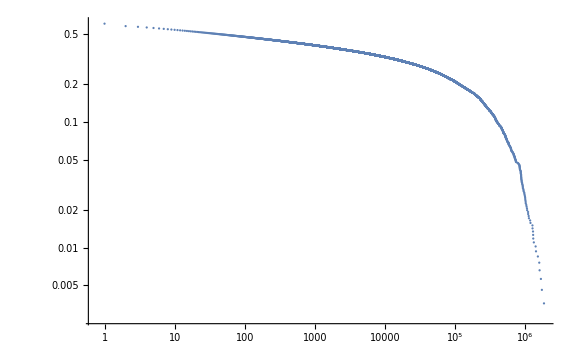

```mathematica
ListLogLogPlot[cumulativeVolume,PlotRange->All,ImageSize->Large]
```

#### Portion of the volume taken up by the top 10% and top 1% of clusters

```mathematica
top10=distribution⟦Length[distribution]-Floor[0.1*Length[distribution]];;⟧;
top01=distribution⟦Length[distribution]-Floor[0.01*Length[distribution]];;⟧;
topSite=Max[sites];
```

```mathematica
Total[top10]⟦1⟧/totalSites//N
Total[top01]⟦1⟧/totalSites//N
topSite/totalSites//N
```

0.231359

0.0791408

0.00125889

#### The fraction of the volume taken up by the top X percent of site sizes

```mathematica
volFraction=Table[
(Total[distribution⟦i;;⟧]⟦1⟧)/(Total[distribution]⟦1⟧),
{i,1,Length[distribution]}];
```

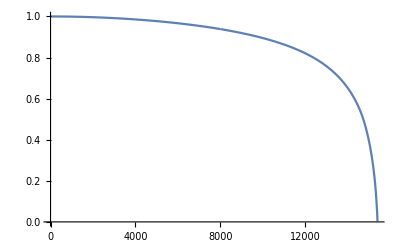

```mathematica
ListLinePlot[volFraction,PlotRange->{0,1}]
```

```mathematica
Max[sites]
```

2014220

```mathematica
aveSize=Sum[distribution⟦i⟧⟦1⟧*distribution⟦i⟧⟦2⟧,{i,1,Length[distribution]}]/Total[counts]//N
```

20.7025